Projekt 2 - Statystyka i teoria obsługi masowej - Dawid Bitner
 1. Opis zjawiska oraz użytego modelu.
 2. Postać symboliczna badanych charakterystyk*. W każdym przypadku należy uwzględnić wartości średnie liczby zgłoszeń ogółem, liczby zgłoszeń w kolejce, czasu przebywania i czasu oczekiwania. Dodatkowe charakterystyki wypisane są przy modelach.
3. Analiza wyników na konkretnych przykładach (zbadanie wpływu parametrów modelu na charakterystyki).

## Odp 1 - Opis zjawiska oraz użytego modelu

M/G/1 - W Biurze Obsługi Studenta pracuje jeden pracownik. BOS przyjmuje średnio λ studentów na godzinę. Napływ studentów do BOS jest zgodny z procesem Poissona. Czas obsługi jednego ze studentów jest zgodny z rozkładem pewnego prawdopodobieństwa (B).

## Odp 2 - Postać symboliczna badanych statystyk

B - czas obsługi klienta,
L - ogólna liczba zgłoszeń
W - czas oczekiwania w kolejce,
S - czas przebywania w systemie kolejki (W+B),
R - pozostały czas obsługi aktualnie obsługiwanego klienta w systemie
L^q - liczba klientów systemu oczekujących na obsługę,
E[x] - wartość oczekiwana (średnia) parametru, 
ρ - obciążenie systemu

```mathematica
Solve[Expected[W]== Expected[L^q]*Expected[B]+x*Expected[R] &&  Expected[L^q]==λ*Expected[W] && x==λ*Expected[B], Expected[R]]
```

{{Expected[R]→(Expected[W]-λ Expected[B] Expected[W])/(λ Expected[B])}}

```mathematica
Solve[Expected[R]==(Expected[W]-λ Expected[B] Expected[W])/(λ Expected[B]), Expected[W]]
```

{{Expected[W]→-(λ Expected[B] Expected[R])/(-1+λ Expected[B])}}

Czas oczekiwania:
E[W]=ρE[R]/(1-ρ)
E[R]=E[B^2]/(2E[B])

Liczba zgłoszeń w kolejce:
E[L^q]=λE[W] (z prawa Little’a)

Czas przebywania w kolejce:
E[S]=E[W] + E[B]

Liczba zgłoszeń ogółem:
E[L]=λ E[S]

Rozkład liczby zgłoszeń:
PC[s_]:=((1-ρ)B̃[λ - λ s](1-s))/(B̃[λ - λ s]-s)

## Odp 3 - Analiza wyników na konkretnych przykładach

```mathematica
ER = EB2/(2EB);
EW[λ_] := (ρ[λ] ER)/(1-ρ[λ]);
ELQ[λ_] := λ EW[λ];
ES[λ_] := EW[λ] + EB;
EL[λ_] := λ ES[λ];
ρ[λ_]:=λ EB; 
TLS[s_]:= LaplaceTransform[PDF[B,t],t, s];
PC[s_] := ((1-ρ[λ])TLS[λ - λ s](1-s))/(TLS[λ - λ s]-s);
```

Rozkład wykładniczy

```mathematica
B = ExponentialDistribution[µ]; 
EB= Expectation[X,X\[Distributed]B]; (* wartość średnia *)
EB2=Expectation[X^2,X\[Distributed]B];(* drugi moment *)
```

#### μ = 13

1/13

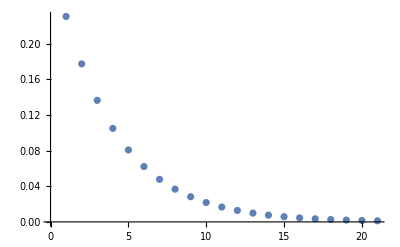

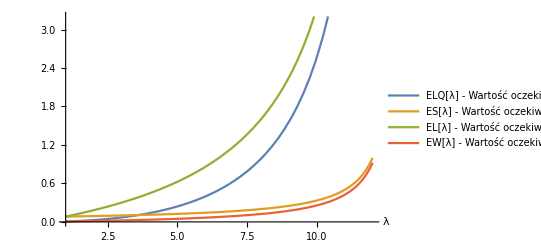

```mathematica
µ=13; 
EB
x := Table[SeriesCoefficient[PC[s]/.λ->10,{s,0,k}], {k,0,20}]
ListPlot[x]
Plot[{ELQ[λ], ES[λ], EL[λ], EW[λ]}, {λ, 1,12},  AxesLabel->Automatic, PlotLegends->{"ELQ[λ] - Wartość oczekiwana liczby klientów czekających na obsługę", "ES[λ] - Wartość oczekiwana czasu przebywania zgłoszenia w systemie", "EL[λ] - Wartość oczekiwana liczby zgłoszeń ogółem", "EW[λ] - Wartość oczekiwana czasu oczekiwania klienta w kolejce"}]
```

#### μ = 30

1/30

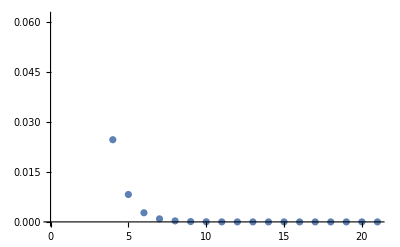

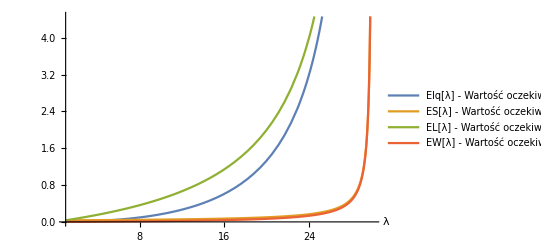

```mathematica
µ=30; 
EB
x := Table[SeriesCoefficient[PC[s]/.λ->10,{s,0,k}], {k,0,20}]
ListPlot[x]
Plot[{ELQ[λ], ES[λ], EL[λ], EW[λ]}, {λ, 1,30},  AxesLabel->Automatic, PlotLegends->{"Elq[λ] - Wartość oczekiwana liczby klientów czekających na obsługę", "ES[λ] - Wartość oczekiwana czasu przebywania zgłoszenia w systemie", "EL[λ] - Wartość oczekiwana liczby zgłoszeń ogółem", "EW[λ] - Wartość oczekiwana czasu oczekiwania klienta w kolejce"}]
```

#### μ = 60

1/60

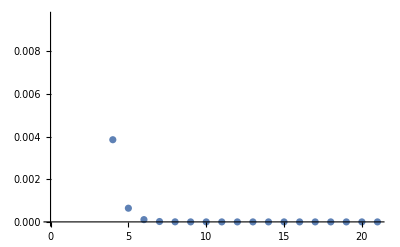

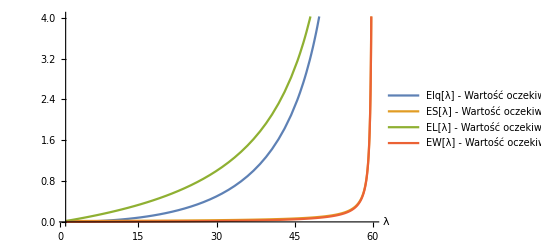

```mathematica
µ=60; 
EB
x := Table[SeriesCoefficient[PC[s]/.λ->10,{s,0,k}], {k,0,20}]
ListPlot[x]
Plot[{ELQ[λ], ES[λ], EL[λ], EW[λ]}, {λ, 1,60},  AxesLabel->Automatic, PlotLegends->{"Elq[λ] - Wartość oczekiwana liczby klientów czekających na obsługę", "ES[λ] - Wartość oczekiwana czasu przebywania zgłoszenia w systemie", "EL[λ] - Wartość oczekiwana liczby zgłoszeń ogółem", "EW[λ] - Wartość oczekiwana czasu oczekiwania klienta w kolejce"}]
```

Rozkład Erlanga

Poniżej przeprowadzono trzy testy dla rozkładu Erlanga ze zmiennym parametrem μ, drugi parametr odpowiada za współczynnik wykorzystywany w rozkładzie Erlanga. Ustawiony został na 100.

```mathematica
ER = EB2/(2EB);
EW[λ_] := (ρ[λ] ER)/(1-ρ[λ]);
ELQ[λ_] := λ EW[λ];
ES[λ_] := EW[λ] + EB;
EL[λ_] := λ ES[λ];
ρ[λ_]:=λ EB; 
TLS[s_]:= LaplaceTransform[PDF[B,t],t, s];
PC[s_] := ((1-ρ[λ])TLS[λ - λ s](1-s))/(TLS[λ - λ s]-s);
```

```mathematica
B =ErlangDistribution[µ, 100];
EB= Expectation[X,X\[Distributed]B]; (* wartość średnia *)
EB2=Expectation[X^2,X\[Distributed]B];(* drugi moment *)
```

#### μ = 13

```mathematica
µ= 13;
```

13/100

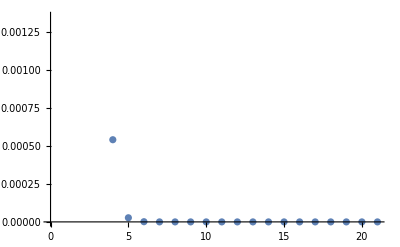

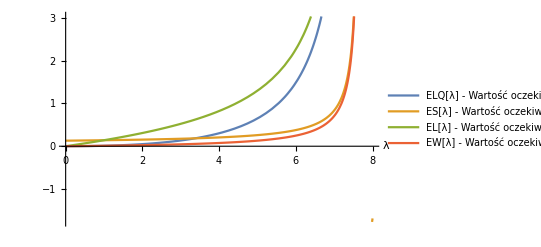

```mathematica
EB 
x := Table[SeriesCoefficient[PC[s]/.λ->1,{s,0,k}], {k,0,20}]
ListPlot[x]

Plot[{ELQ[λ], ES[λ], EL[λ], EW[λ]}, {λ, 0,8},  AxesLabel->Automatic, PlotLegends->{"ELQ[λ] - Wartość oczekiwana liczby klientów czekających na obsługę", "ES[λ] - Wartość oczekiwana czasu przebywania zgłoszenia w systemie", "EL[λ] - Wartość oczekiwana liczby zgłoszeń ogółem", "EW[λ] - Wartość oczekiwana czasu oczekiwania klienta w kolejce"}]
```

#### μ = 30

```mathematica
µ=30;
```

3/10

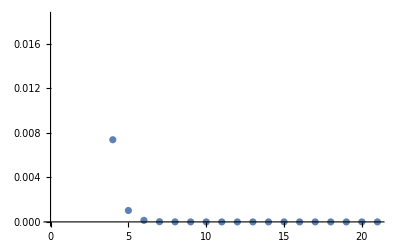

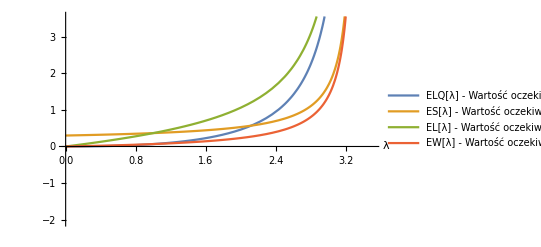

```mathematica
EB 
x := Table[SeriesCoefficient[PC[s]/.λ->1,{s,0,k}], {k,0,20}]
ListPlot[x]
Plot[{ELQ[λ], ES[λ], EL[λ], EW[λ]}, {λ, 0,3.5},  AxesLabel->Automatic, PlotLegends->{"ELQ[λ] - Wartość oczekiwana liczby klientów czekających na obsługę", "ES[λ] - Wartość oczekiwana czasu przebywania zgłoszenia w systemie", "EL[λ] - Wartość oczekiwana liczby zgłoszeń ogółem", "EW[λ] - Wartość oczekiwana czasu oczekiwania klienta w kolejce"}]
```

#### μ = 60

```mathematica
µ=60;
```

3/5

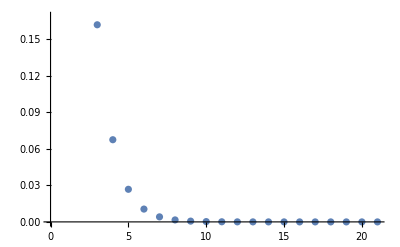

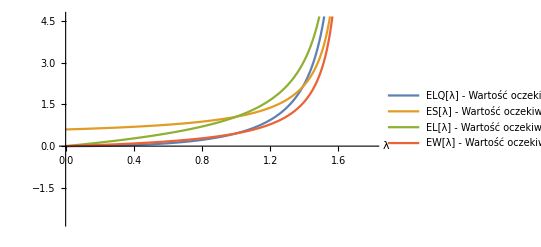

```mathematica
EB 
x := Table[SeriesCoefficient[PC[s]/.λ->1,{s,0,k}], {k,0,20}]
ListPlot[x]
Plot[{ELQ[λ], ES[λ], EL[λ], EW[λ]}, {λ, 0,1.8},  AxesLabel->Automatic, PlotLegends->{"ELQ[λ] - Wartość oczekiwana 7iczby klientów czekających na obsługę", "ES[λ] - Wartość oczekiwana czasu przebywania zgłoszenia w systemie", "EL[λ] - Wartość oczekiwana liczby zgłoszeń ogółem", "EW[λ] - Wartość oczekiwana czasu oczekiwania klienta w kolejce"}]
```

## Wnioski

Zarówno w przypadku rozkładu wykładniczego jak i rozkładu Erlanga wraz ze wzrostem intensywności napływu zgłoszeń (λ) maleje ogólna wydajność systemu. Wpływ na to ma również intensywność obsługi zgłoszeń - czyli informacja o ogólnej wydajności systemu na starcie (μ). Czyli, wraz ze wzrostem obciążenia systemu dla powyższych rozkładów maleje jego wydajność. Zwiększając parametr μ  dla rozkładu wykładniczego możemy zaobserwować, że system zaczyna być “później” mniej wydajny, niż gdy parametr ten jest mniejszy. W przypadku rozkładu Erlanga jest odwrotnie - zwiększając parametr µ system zaczyna być szybciej mniej wydajny . W obu przypadkach rosną wszystkie wartości: wartość oczekiwana liczby klientów czekających na obsługę, wartość oczekiwana czasu przebywania zgłoszenia w systemie, wartość oczekiwana liczby zgłoszeń ogółem i wartość oczekiwana czasu oczekiwania klienta w kolejce. W przypadku rozkładu Erlanga można zauważyć, że wszystkie z tych wzrostów rozpoczynają się mniej więcej w podobny miejscu na osi X (są bliżej siebie) jeżeli zwiększymy parametr µ, natomiast w przypadku rozkładu wykładniczego w pewnym momencie (“dalej” na osi X niż pozostałe) wartość oczekiwana czasu oczekiwania klienta w kolejce zaczyna bardzo szybko wzrastać, zwiększając zakresy na wykresie można zauważyć, że zbliża się do wartości krytycznej oznaczającej ogólną niewydajność systemu (zbliża się do nieskończoności). Wnioskiem który nie będzie szczególnie odkrywczy będzie również informacja o tym, że czym system bardziej obciążony i ma mniejszą “moc przerobową” - tym wolniej obsługuje zdarzenia - różnice są zauważalne w tempie spadku wydajności np.: poprzez długość oczekiwania klienta w kolejce.